```mathematica
Clear[m,n]
```

```mathematica
$Assumptions={m,n}∈PositiveIntegers;
```

### Experiment

```mathematica
RandomSim[p0_, o0_, dis0_, w0_, m0_, n0_]:= Module[{p=p0, w=w0, m=m0, n=n0, o=o0, dis=dis0},
f[{p_,o_}]:=dis[[p,o]];
Life[alloc_]:=Total[f/@alloc];
Wait[p_,alloc_]:=Total[w[[Complement[p,alloc[[All,1]]]]]];
Goal[p_,alloc_]:=Wait[p,alloc]+Life[alloc];
NormlizedGoal[p_,alloc_]:=Goal[p,alloc]-Total[w[[p]]];
RandomAlloc[p_,o_]:=MapIndexed[If[#2[[1]]<=w[[#1[[1]]]]&&f[#1]>w[[#2[[1]]]],#1,Nothing]&,{RandomSample[p][[;;Min[m,n]]],RandomSample[o][[;;Min[m,n]]]}ᵀ];
SampleGoal[p,o]:={Goal[p,#], #}&@RandomAlloc[p,o];
smps=Table[{#[[1]]/n, #[[2]]}& @SampleGoal[p,o],(m+n)^2];
scores = #[[1]]&/@smps;
allocations = #[[2]] &/@smps;
{scores, allocations}
]
```

```mathematica
OptimalSim[p0_, o0_, dis0_, w0_, m0_, n0_]:= Module[{p=p0, w=w0, m=m0, n=n0, o=o0, dis=dis0},
T = Min[m, n];
var[i_,j_, t_] := Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t];
waitConstr[w_, i_] :=  Table[Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t] == 0, {j, m}, {t, w+1, T}] // Flatten;
EvaluateSolution[alloc_]:= (Total[dis[[#[[1]],#[[2]]]] & /@alloc] + (w[[Complement[p, #[[1]] &/@alloc]]] // Total))/n;
obj1 = Table[-dis[[i,j]]*var[i,j,t], {i,  n}, {j,  m}, {t, T}] // Flatten // Total;
obj2 = Table[-w[[i]] * (1 - (Table[var[i,j,t], {j, m},{t, T}] // Flatten // Total )), {i, n}]  // Total;
obj = obj1 + obj2;
constr = Table[(Flatten[Table[var[i,j,t], {j, m},{t, T}] ] // Total) <= 1, {i, n}];
constr2 = Table[( Flatten[Table[var[i,j,t], {i, n}, {t, T}]] //Total) <= 1, {j, m}];
constr3 = Table[ (Flatten[Table[var[i,j,t], {i, n}, {j, m}]] //Total)<= 1, {t, T}];
constr4 = Table[var[i,j,t] >= 0, {i, n}, {j, m}, {t, T}] // Flatten;
constr5 = waitConstr[#[[1]], #[[2]]]&/@Transpose[{w, p}] // Flatten;
res = LinearOptimization[obj1+obj2, constr~Join~constr2~Join~constr3~Join~constr4~Join~constr5, Table[var[i,j,t]∈ Integers, {i, n}, {j, m}, {t, T}]//Flatten];
SplitRes[s_]:= ToString@s// StringSplit[#, "x"]& // StringSplit[#, "d"]& //ToExpression// Flatten;
ExtractAllocation[res_]:=SortBy[SplitRes[#[[1]]] & /@ Select[res, (#[[2]] == 1&)], Last];
alloc = ExtractAllocation[res];
{EvaluateSolution[alloc], alloc}
];



Sim[n0_, m0_]:= Module[{n=n0, m=m0},
p=Range[n];
o=Range[m];
w=RandomVariate[PoissonDistribution[15],n];
pZ=RandomVariate[NormalDistribution[0,10],n];
oZ=RandomVariate[NormalDistribution[0,10],m];
dis=5Ramp[DistanceMatrix[pZ,oZ]-5];
randomScores = RandomSim[p, o, dis, w, m, n][[1]];
optimalScore = OptimalSim[p, o, dis, w, m, n][[1]];
{Max[randomScores], optimalScore}
];
```

```mathematica
Sim[5, 5]
```

{41.5797,41.5797}

```mathematica
ratios = Table[Table[#[[2]] / #[[1]]&@Sim[n,n], 2]//Mean, {n,5, 60, 5}]
```

{1.,1.05329,1.08825,1.19763,1.345,1.37724,1.5418,1.58629,1.61019,1.6895,1.69296,1.71376}

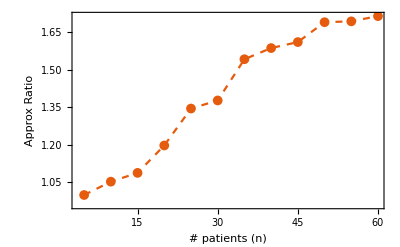

```mathematica
ListLinePlot[Transpose[{Range[5, 60, 5], ratios}],PlotRange->Full,Frame->True,FrameLabel->{"# patients (n)","Approx Ratio"},LabelStyle->{FontSize->18,FontColor->Black,FontFamily->"CMU Sans Serif"},PlotTheme->"Scientific",PlotMarkers->{Automatic, 10},PlotStyle->Dashed]
```

```mathematica
Histogram[scores,50,"Probability",Frame->True,FrameLabel->{"Years of Life Added Per Patient","Probability"},LabelStyle->{FontSize->18,FontColor->Black,FontFamily->"CMU Sans Serif"},PlotTheme->"Scientific",AspectRatio->1/4]
```